```mathematica
Clear[y1]
Solve[12== 1/(y1/7.286-(1-y1)/515.74),y1]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{y1→0.612639}}

```mathematica
Exp[20/(83.14*288.15)*(-455.18+(0.627^2*(2*-92.46+25.88+282.36)))]
```

0.712107

```mathematica
Clear[x1]
x2=1-x1
Solve[Exp[19.71*(1-x1)^2]*0.3543== Exp[19.71*x1^2]*0.3726,x1]
```

1-x1

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x1→0.498722}}

19.71

1.95947

1.14854

35.43

37.26

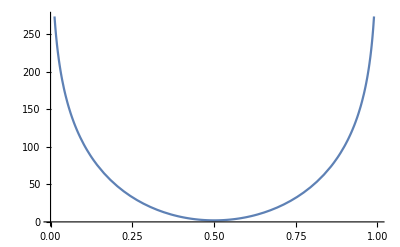

```mathematica
A=19.71
γ1=Log[A*x2^2]
γ2= Log[A*x1^2]
P1=35.43
P2=37.26
Plot[60==35.43 x1 Log[19.71 (1-x1)^2]+37.26 (1-x1) Log[19.71 x1^2],{x1,0,1}]
```

```mathematica
V=449.8-L
Solve[0.15*449.8== 0.4*L+0.6*V,L]
```

449.8-L

{{L→1012.05}}

```mathematica
Clear[V,L]
NSolve[{0.15*449.8== 0.4*L+0.6*V,0.85*449.8== 0.6*L+0.4*V},{V,L}]
```

{{V→-562.25,L→1012.05}}

```mathematica
A=1.2

NSolve[{A*(1-α)^2-A*(1-β)^2== Log[β/α],A*α^2-A*β^2== Log[(1-β)/(1-α)]},{α,β}]
```

1.2

```mathematica
x1=0.4
x2=0.6
A=0.918
B=1.148
γ1=Exp[A/(1+(A*x1)/(B*x2))^2]
γ2=Exp[B/(1+(B*x2)/(A*x1))^2]
```

0.4

0.6

0.918

1.148

1.47783

1.14891

```mathematica
P1=37.126
P2=24.398

x1*γ1*P1+x2*γ2*P2
```

37.126

24.398

38.7649

```mathematica
A=1.2

NSolve[{A*(1-α)^2-A*(1-β)^2== Log[β/α],A*α^2-A*β^2== Log[(1-β)/(1-α)]},{α,β}]
```

1.2